## Importing importing Libraries and declaring initial variables

```mathematica
<<Teukolsky` ;
<<SimulationTools`;
SetEnvironment["PATH"->Environment["PATH"]<>";"<>"C:\\Users\\student\\anaconda3"];
SetEnvironment["PATH"->Environment["PATH"]<>";"<>"C:\\Users\\student\\anaconda3\\Library\\bin"];
session=StartExternalSession[<|"System"->"Python","Executable"->"C:\\Users\\student\\anaconda3\\python.exe"|>];
py=ExternalEvaluate[session];
py["import sxs"];
```

```mathematica
py["catalog = sxs.load(\"catalog\")"]
sims=py["catalog.simulations_dataframe"]


SXSWaveform[id_,{l_Integer,m_Integer}]:=Module[{time,waveform},
py["w = sxs.load(\""<>id<>"/Lev/rhOverM\", extrapolation_order = 2)"];
{time,waveform}=Normal/@py["(w.t, w[:, w.index("<>ToString[l]<>", "<>ToString[m]<>")])"];
ToDataTable[time,waveform]
]
```

Skipping download from 'https://data.black-holes.org/catalog.json' because local file is newer

Dataset[<>]

```mathematica
h22=SXSWaveform["SXS:BBH:0064",{2,2}]
```

```mathematica
m1=sims["SXS:BBH:0064"]["initial_mass1"];
m2=sims["SXS:BBH:0064"]["initial_mass2"];
```

```mathematica
ν=(m1 m2)/(m1+m2)^2;
```

```mathematica
M=m1+m2;
m=2;
```

Importing the Flux and the h22 amplitudes

```mathematica
ℱ=Interpolation[Import["kerra05_1.mx"],InterpolationOrder->8];
ℱπ=Interpolation[Import["kerra05_pi.mx"],InterpolationOrder->8];
ℱ1=Interpolation[Import["kerra09.mx"],InterpolationOrder->8];
ℱ1π=Interpolation[Import["kerra09_pi.mx"],InterpolationOrder->8];
ℱ2 =Interpolation[,InterpolationOrder->8];
ℱ2π =Interpolation[Import["kerra00_pi.mx"],InterpolationOrder->8];
```

```mathematica
hAmp=Interpolation[Import["h2205m.mx"],InterpolationOrder->8];

Interpolation[Phase[h22]][0]
Ωinit=sims["SXS:BBH:0064"]["initial_orbital_frequency"]
ϕinit=0
r0init=(M Ωinit)^(-2/3)


Normal[sims["SXS:BBH:0064"]["reference_dimensionless_spin1"]]
```

## Computing Inspiral

```mathematica
a=0.5;

{Ωsol,ϕsol,r0sol}=NDSolveValue[{
Ω0'[t]==(3 (-3 M/r0[t]+2 a Sqrt[M/r0[t]^3]+1)^(3/2) ν ℱ[r0[t]])/((a Sqrt[M/r0[t]^3]+1)^2 Sqrt[M/r0[t]^3]((8 a Sqrt[M/r0[t]^3]+1) r0[t]^2 -6 M r0[t] -3 a^2)),
ϕ0'[t]==Ω0[t],
Ω0[t]==Sqrt[M/r0[t]^3]/(1+a Sqrt[M/r0[t]^3]),
r0[0]==r0init,
ϕ0[0]==ϕinit,
WhenEvent[r0[t]≤6.01M, "StopIntegration"]},{Ω0,ϕ0,r0},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];

{tmin,tmax}=r0sol["Domain"][[1]];


{Ωπsol,ϕπsol,r0πsol}=NDSolveValue[{
Ω0'[t]==(3 (-3 M/r0[t]+2 a Sqrt[M/r0[t]^3]+1)^(3/2) ν ℱπ[r0[t]])/((a Sqrt[M/r0[t]^3]+1)^2 Sqrt[M/r0[t]^3]((8 a Sqrt[M/r0[t]^3]+1) r0[t]^2 -6 M r0[t] -3 a^2)),
ϕ0'[t]==Ω0[t],
Ω0[t]==Sqrt[M/r0[t]^3]/(1+a Sqrt[M/r0[t]^3]),
r0[0]==r0init,
ϕ0[0]==ϕinit,
WhenEvent[r0[t]≤6.01M, "StopIntegration"]},{Ω0,ϕ0,r0},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];

{tminπ,tmaxπ}=r0πsol["Domain"][[1]];
```

InterpolatingFunction::dmval: Input value {5.99916} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
{{a=0.9;

{Ω1πsol,ϕ1πsol,r01πsol}=NDSolveValue[{
Ω01'[t]==(3 (-3 M/r01[t]+2 a Sqrt[M/r01[t]^3]+1)^(3/2) ν ℱ1π[r01[t]])/((a Sqrt[M/r01[t]^3]+1)^2 Sqrt[M/r01[t]^3]((8 a Sqrt[M/r01[t]^3]+1) r01[t]^2 -6 M r01[t] -3 a^2)),
ϕ01'[t]==Ω01[t],
Ω01[t]==Sqrt[M/r01[t]^3]/(1+a Sqrt[M/r01[t]^3]),
r01[0]==r0init,
ϕ01[0]==ϕinit,
WhenEvent[r01[t]≤6.01M, "StopIntegration"]},{Ω01,ϕ01,r01},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];

{tmin1,tmax1}=r01sol["Domain"][[1]];}, {{Ω1sol,ϕ1sol,r01sol}=NDSolveValue[{
Ω01'[t]==(3 (-3 M/r01[t]+2 a Sqrt[M/r01[t]^3]+1)^(3/2) ν ℱ1[r01[t]])/((a Sqrt[M/r01[t]^3]+1)^2 Sqrt[M/r01[t]^3]((8 a Sqrt[M/r01[t]^3]+1) r01[t]^2 -6 M r01[t] -3 a^2)),
ϕ01'[t]==Ω01[t],
Ω01[t]==Sqrt[M/r01[t]^3]/(1+a Sqrt[M/r01[t]^3]),
r01[0]==r0init,
ϕ01[0]==ϕinit,
WhenEvent[r01[t]≤6.01M, "StopIntegration"]},{Ω01,ϕ01,r01},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];

{tmin1π,tmax1π}=r01πsol["Domain"][[1]];}}
```

InterpolatingFunction::dmval: Input value {5.99661} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{Null^3},{Null^2}}

```mathematica
~
```

{{Null^3},{Null^2}}

```mathematica
a=0;

{Ω2sol,ϕ2sol,r02sol}=NDSolveValue[{
Ω02'[t]==(3 (-3 M/r02[t]+2 a Sqrt[M/r02[t]^3]+1)^(3/2) ν ℱ2[r02[t]])/((a Sqrt[M/r02[t]^3]+1)^2 Sqrt[M/r02[t]^3]((8 a Sqrt[M/r02[t]^3]+1) r02[t]^2 -6 M r02[t] -3 a^2)),
ϕ02'[t]==Ω02[t],
Ω02[t]==Sqrt[M/r02[t]^3]/(1+a Sqrt[M/r02[t]^3]),
r02[0]==r0init,
ϕ02[0]==ϕinit,
WhenEvent[r02[t]≤6.01M, "StopIntegration"]},{Ω02,ϕ02,r02},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];

{tmin2,tmax2}=r02sol["Domain"][[1]];

{Ω2πsol,ϕ2πsol,r02πsol}=NDSolveValue[{
Ω02'[t]==(3 (-3 M/r02[t]+2 a Sqrt[M/r02[t]^3]+1)^(3/2) ν ℱ2π[r02[t]])/((a Sqrt[M/r02[t]^3]+1)^2 Sqrt[M/r02[t]^3]((8 a Sqrt[M/r02[t]^3]+1) r02[t]^2 -6 M r02[t] -3 a^2)),
ϕ02'[t]==Ω02[t],
Ω02[t]==Sqrt[M/r02[t]^3]/(1+a Sqrt[M/r02[t]^3]),
r02[0]==r0init,
ϕ02[0]==ϕinit,
WhenEvent[r02[t]≤6.01M, "StopIntegration"]},{Ω02,ϕ02,r02},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];

{tmin2π,tmax2π}=r02πsol["Domain"][[1]];
```

Evolution of r0

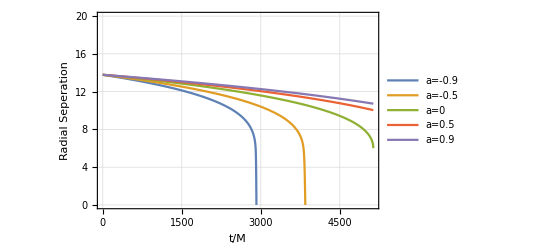

sxsbbh0065evolution.png

```mathematica
p1=Plot[{r01πsol[t],r0πsol[t],r02sol[t],r0sol[t],r01sol[t]},
{t,tmin2,tmax2},PlotRange->{0,20},ImageSize->400,GridLines->Automatic,PlotStyle->{"Red","Green","Blue","Black","Dashed"},PlotLegends->Placed[{"a=-0.9","a=-0.5","a=0","a=0.5","a=0.9"},{Left,Bottom}],AxesLabel->{Time},Frame->True,FrameLabel->{"t/M","Radial Seperation"}]

Export["sxsbbh0065evolution.png",p1]
```

Evolution of Orbital Frequency

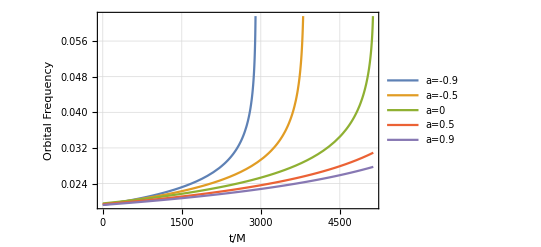

sxsbbh0065frequency.png

```mathematica
p2=Plot[{Ω1πsol[t],Ωπsol[t],Ω2sol[t],Ωsol[t],Ω1sol[t]},
{t,tmin2,tmax2},ImageSize->400,GridLines->Automatic,
PlotLegends->Placed[{"a=-0.9","a=-0.5","a=0","a=0.5","a=0.9"},{Left,Top}],FrameLabel->{"t/M","Orbital Frequency"},Frame->True]

Export["sxsbbh0065frequency.png",p2]
```

Evolution of Orbital Phase

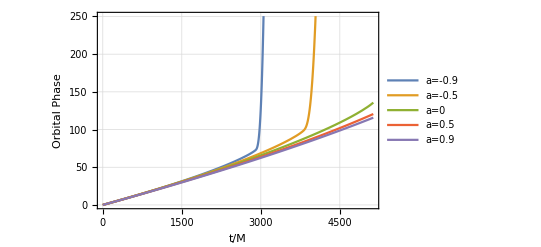

sxsbbh0065phaseevolution.png

```mathematica
p3=Plot[{ϕ1πsol[t],ϕπsol[t],ϕ2sol[t],ϕsol[t],ϕ1sol[t]},{t,tmin2,tmax2},GridLines->Automatic,Frame->True,ImageSize->400,PlotLegends->Placed[{"a=-0.9","a=-0.5","a=0","a=0.5","a=0.9"},{Left,Top}],AxesLabel->{Time},Frame->True,FrameLabel->{"t/M","Orbital Phase"}];
p3
Export["sxsbbh0065phaseevolution.png",p3]
```

## Computing the Waveform

```mathematica
fixer=Interpolation[Phase[h22]][0]
𝓂=2;
h[t_]:=ν hAmp[r0sol[t]] ⅇ^(-ⅈ (𝓂 ϕsol[t]+Arg[hAmp[r0sol[0]]]+fixer));
h1[t_]:=ν hAmp[r01sol[t]] ⅇ^(-ⅈ (𝓂 ϕ1sol[t]+Arg[hAmp[r01sol[0]]]+fixer));
h2[t_]:=ν hAmp[r02sol[t]] ⅇ^(-ⅈ (𝓂 ϕ2sol[t]+Arg[hAmp[r02sol[0]]]+fixer));
hπ[t_]:=ν hAmp[r0πsol[t]] ⅇ^(-ⅈ (𝓂 ϕπsol[t]+Arg[hAmp[r0πsol[0]]]+fixer));
h1π[t_]:=ν hAmp[r01πsol[t]] ⅇ^(-ⅈ (𝓂 ϕ1πsol[t]+Arg[hAmp[r01πsol[0]]]+fixer));
```

-3.37718

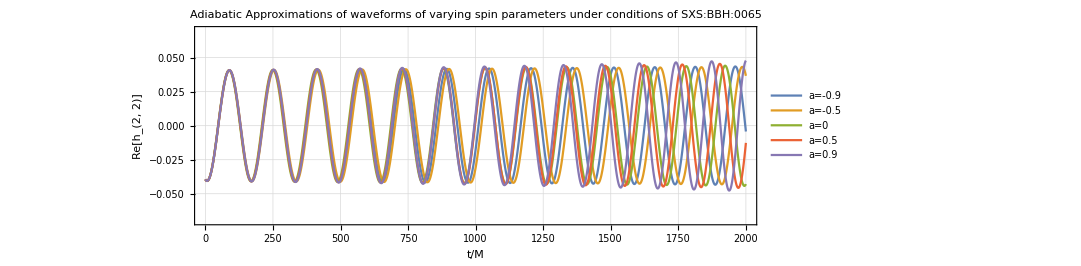

sxsbbh0065approximations.png

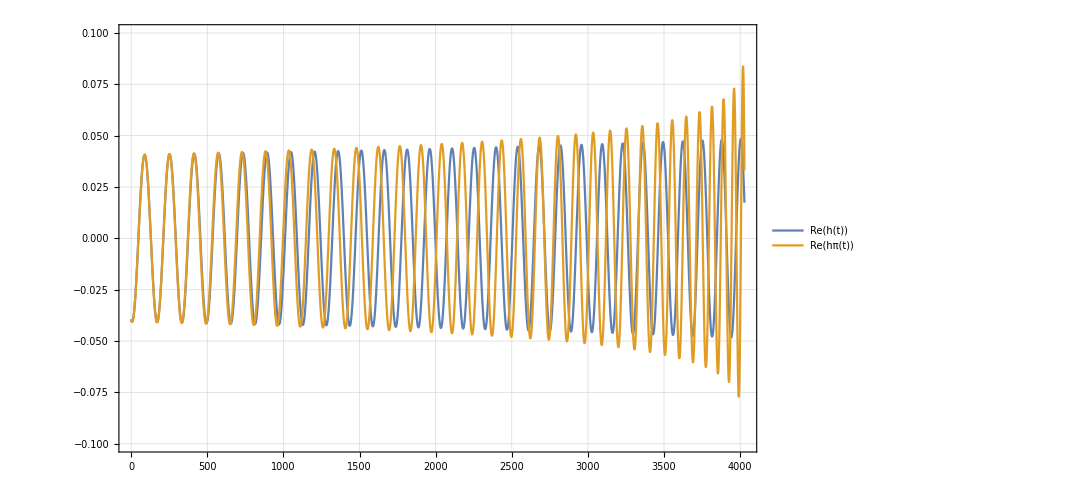

```mathematica
p5=Plot[{Re[h[t]],Re[h1[t]],Re[h2[t]],Re[hπ[t]],Re[h1π[t]]},{t,tmin2,2000},PlotRange->{-0.07,0.07},ImageSize->800,GridLines->Automatic,
PlotLabel->"Adiabatic Approximations of waveforms of varying spin parameters under conditions of  SXS:BBH:0065",
PlotLegends->Placed[{"a=-0.9","a=-0.5","a=0","a=0.5","a=0.9"},Above],FrameLabel->{"t/M","Re[h_(2, 2)]"},Frame->True,AspectRatio->1/3]

Export["sxsbbh0065approximations.png",p5]
Plot[{Re[h[t]],Re[hπ[t]]},{t,tminπ,tmaxπ},PlotRange->{-0.1,0.1},ImageSize->800,PlotTheme->"Detailed"]
```

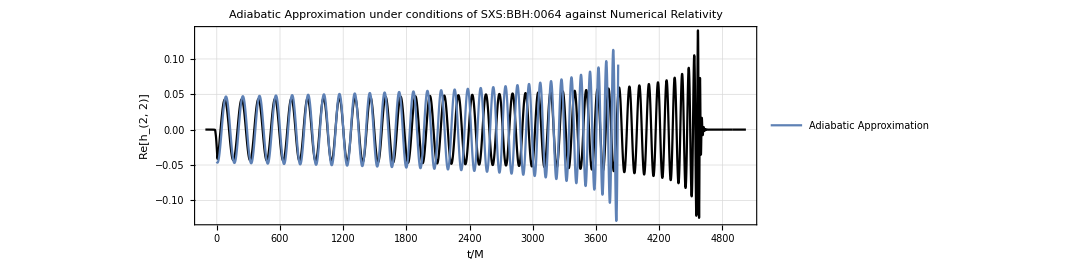

```mathematica
p8=Show[ListLinePlot[Re[h22],PlotTheme->"Detailed",FrameLabel->{"t/M","Re[h_(2, 2)]"},PlotStyle->Black],Plot[{Re[hπ[t]]},{t,tminπ,tmaxπ},PlotPoints->90,PlotLegends->Placed[{"Adiabatic Approximation"},{Left,Top}]],PlotRange->All,ImageSize->800,PlotLabel->"Adiabatic Approximation under conditions of SXS:BBH:0064 against Numerical Relativity",AspectRatio->1/3]

Export["sxsbbh0064vsnumericalrelativity.png",p8]
```

```mathematica
phase00[t_] :=-(𝓂 ϕ2sol[t]+Arg[hAmp[r02sol[0]]])+fixer+Arg[hAmp[r02sol[t]]]

phase05[t_] :=-(𝓂 ϕsol[t]+Arg[hAmp[r0sol[0]]])+fixer+Arg[hAmp[r0sol[t]]]
phase09[t_] :=-(𝓂 ϕ1sol[t]+Arg[hAmp[r01sol[0]]])+fixer+Arg[hAmp[r01sol[t]]]
phase05m[t_] :=-(𝓂 ϕπsol[t]+Arg[hAmp[r0πsol[0]]])+fixer+Arg[hAmp[r0πsol[t]]]
phase09m[t_] :=-(𝓂 ϕ1πsol[t]+Arg[hAmp[r01πsol[0]]])+fixer+Arg[hAmp[r01πsol[t]]]
```

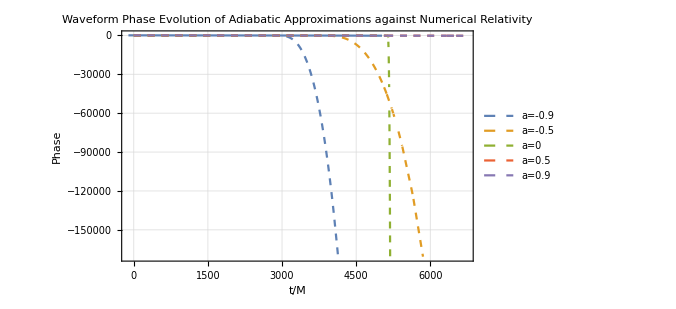

sxsbbh0064phasevolution.png

```mathematica
p27=Show[ListLinePlot[Phase[h22]],Plot[{phase09m[t],phase05m[t],phase00[t],phase05[t],phase09[t]},{t,tmin,tmax},PlotStyle->Dashed,PlotLegends->Placed[{"a=-0.9","a=-0.5","a=0","a=0.5","a=0.9"},{Left,Bottom}],FrameLabel->{"Time"}],PlotTheme->"Detailed",ImageSize->500,PlotLabel->"Waveform Phase Evolution of Adiabatic Approximations against Numerical Relativity",GridLines->Automatic,Frame->True,FrameLabel->{"t/M","Phase"},PlotRange->{{0,5000},{0,-500}}]

Export["sxsbbh0064phasevolution.png",p27]
```

InterpolatingFunction::dmval: Input value {-108.245} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3590.09} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-108.245} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2200.43} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-108.245} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2862.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-108.245} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-270.658} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-108.245} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3645.26} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

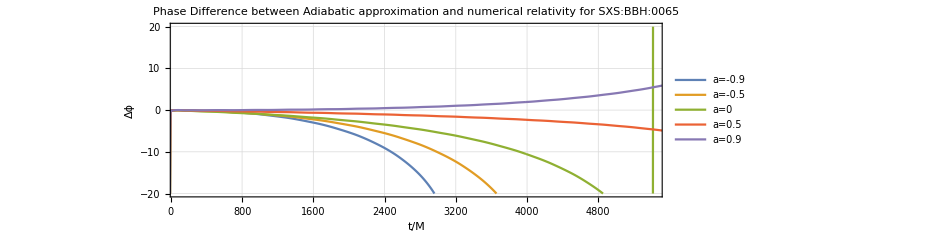

sxsbbh0065phasediff.PNG

```mathematica
p00=Map[phase00,Coordinate[Phase[h22]]];
p05=Map[phase05,Coordinate[Phase[h22]]];
p09=Map[phase09,Coordinate[Phase[h22]]];
p05m=Map[phase05m,Coordinate[Phase[h22]]];
p09m=Map[phase09m,Coordinate[Phase[h22]]];

p12=ListLinePlot[{p09m-Phase[h22],p05m-Phase[h22],p00-Phase[h22],p05-Phase[h22],p09-Phase[h22]},PlotRange->{{100,tmax2},{-20,20}},PlotLegends->Placed[{"a=-0.9","a=-0.5","a=0","a=0.5","a=0.9"},{Left,Bottom}],PlotTheme->"Detailed",PlotLabel->"Phase Difference between Adiabatic approximation and numerical relativity for SXS:BBH:0065",ImageSize->700,FrameLabel->{"t/M","Δϕ"},AspectRatio->1/3,Frame->True]

Export["sxsbbh0065phasediff.PNG",p12]
```

DataTable[<17242>,{{-108.246,5022.83}}]

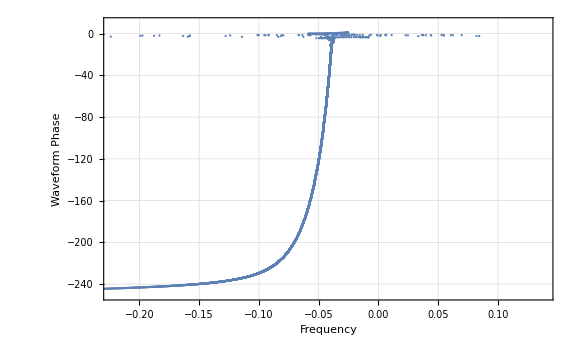

```mathematica
ListPlot[ToDataTable[Frequency[h22],Phase[h22]],ImageSize->Large,PlotTheme->"Detailed",PlotRange->{-250,10},FrameLabel->{"Frequency","Waveform Phase"}]
```

```mathematica
freq00[t_] :=Evaluate[Re[D[-(𝓂 ϕ2sol[t]+Arg[hAmp[r02sol[0]]])+fixer+Arg[hAmp[r02sol[t]]],t]]]
freq05[t_] :=Evaluate[Re[D[-(𝓂 ϕsol[t]+Arg[hAmp[r0sol[0]]])+fixer+Arg[hAmp[r0sol[t]]],t]]]
freq09[t_] :=Evaluate[Re[D[-(𝓂 ϕ1sol[t]+Arg[hAmp[r01sol[0]]])+fixer+Arg[hAmp[r01sol[t]]],t]]]
freq05m[t_] :=Evaluate[Re[D[-(𝓂 ϕπsol[t]+Arg[hAmp[r0πsol[0]]])+fixer+Arg[hAmp[r0πsol[t]]],t]]]
freq09m[t_] :=Evaluate[Re[D[-(𝓂 ϕ1πsol[t]+Arg[hAmp[r01πsol[0]]])+fixer+Arg[hAmp[r01πsol[t]]],t]]]
```

```mathematica
List@@D[Arg[hAmp[r02sol[t]]],t]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][InterpolatingFunction[…][t]],Arg'[InterpolatingFunction[…][InterpolatingFunction[…][t]]]}

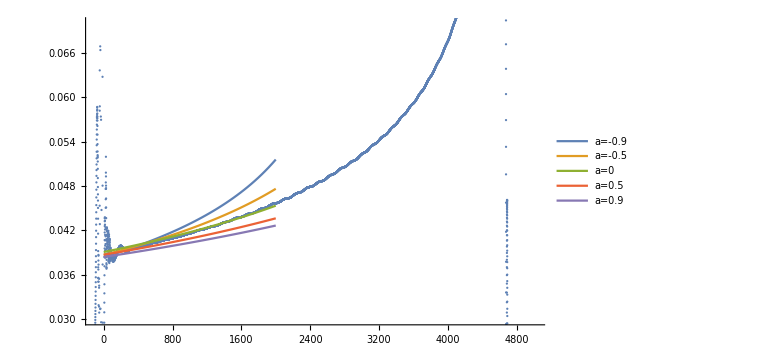

DataTable[<24349>,{{-108.245,7985.57}}]

```mathematica
Show[ListPlot[-Frequency[h22]],Plot[{-freq09m[t],-freq05m[t],-freq00[t],-freq05[t],-freq09[t]},{t,0,2000},PlotLabel->"Frequency",PlotLegends->{"a=-0.9","a=-0.5","a=0","a=0.5","a=0.9"}],PlotRange->{0.03,0.07},ImageSize->Large]
```

```mathematica
h22Amp=Interpolation[Import["h2205.mx"],InterpolationOrder->8];
h33Amp=Interpolation[Import["h3305.mx"],InterpolationOrder->8];
h44Amp=Interpolation[Import["h4405.mx"],InterpolationOrder->8];
h55Amp=Interpolation[Import["h5505.mx"],InterpolationOrder->8];
```

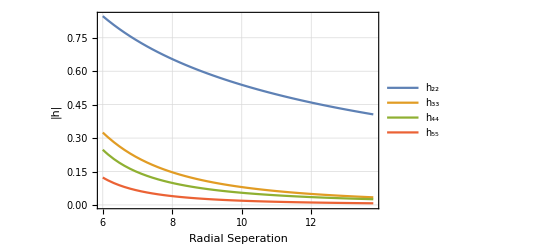

```mathematica
p68=Plot[{Re[h22Amp[r]],Re[h33Amp[r]],Re[Abs[h44Amp[r]]],Re[Abs[h55Amp[r]]]},{r,6,r0init},GridLines->Automatic,Frame->True,FrameLabel->{"Radial Seperation","|h|"},PlotLegends->Placed[{"h_22","h_33","h_44","h_55"},{Right,Top}]]
```

```mathematica
Export["flux_amplitudes.png",p68]
```

flux_amplitudes.png

```mathematica
h00Amp=Interpolation[Import["h22.mx"],InterpolationOrder->8];
h05mAmp=Interpolation[Import["h2205m.mx"],InterpolationOrder->8];
h09Amp=Interpolation[Import["h2209.mx"],InterpolationOrder->8];
```

```mathematica
h09mAmp=Interpolation[Import["h2209m.mx"],InterpolationOrder->8];
```

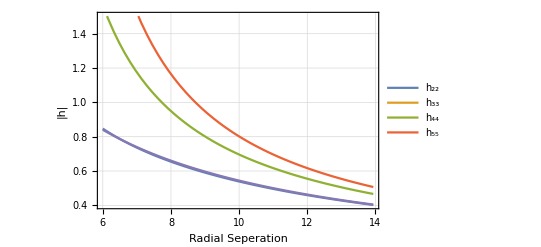

```mathematica
p69=Plot[{Re[h22Amp[r]],Re[Abs[h05Amp[r]]],Re[Abs[h05mAmp[r]]],Re[Abs[h09mAmp[r]]],Re[Abs[h09Amp[r]]]},{r,6,r0init},GridLines->Automatic,Frame->True,FrameLabel->{"Radial Seperation","|h|"},PlotLegends->Placed[{"h_22","h_33","h_44","h_55"},{Right,Top}]]
```